## Baye’s Theorem - flipping a coin and fairness

How an evidence change our belief in the fairness of the coin

General Baye's theorem formulation :

```mathematica
PosteriorP(θ,D)=(PriorP(θ) LikelihoodP[D,θ])/(EvidenceP(D))
```

We detail the construction of the different piece of the Baye’s theorem in case of our coin experiment with the Bernoulli distribution

## First the Beta function

Used in the definition of the Prior belief function

(BetaS because Mathematica has already the Beta function defined)

```mathematica
BetaS[α_,β_] = ∫_0^1 x^(α-1)(1-x)^(β-1)ⅆx
```

ConditionalExpression[(Gamma[α] Gamma[β])/Gamma[α+β], Re[α]>0&&Re[β]>0]

```mathematica
1/BetaS[α, β]
```

ConditionalExpression[Gamma[α+β]/(Gamma[α] Gamma[β]), Re[α]>0&&Re[β]>0]

## Prior probability function (density)

```mathematica
PriorP[x_, α_, β_] := ((1-x)^(-1+β) x^(-1+α))/BetaS[α,β]
```

```mathematica
PriorP[x, α, β]
```

ConditionalExpression[((1-x)^(-1+β) x^(-1+α) Gamma[α+β])/(Gamma[α] Gamma[β]), Re[α]>0&&Re[β]>0]

```mathematica
Animate[Plot[PriorP[x, α, β], {x,0,1},
PlotRange->All,
PlotLabel->"α = " <>ToString[α] <> "  " <> "β = " <> ToString[β]],
{α, 1, 50, 1},
{β, 1,50, 1}, 
AnimationRunning->False]
```

## The likelihood of the evidence

The event n flips with k heads will be formalized as the couple n,k
Then we want to define the probability function of this event when the fairness of the coin is known as θ, the likelihood probability function is:

```mathematica
LikelihoodP[n_, k_, θ_] := θ^k(1-θ)^(n-k)
```

## The probability of the Evidence

```mathematica
EvidenceP[n_, k_,  α_,β_] := ∫_0^1 LikelihoodP[n,k,θ] PriorP[θ,α,β] ⅆθ
```

```mathematica
EvidenceP[n, k,  α, β]
```

ConditionalExpression[(Gamma[k+α] Gamma[-k+n+β] Gamma[α+β])/(Gamma[α] Gamma[β] Gamma[n+α+β]), Re[α]>0&&Re[β]>0&&Re[k]<Re[n+β]&&Re[k+α]>0]

## The Posterior probability

```mathematica
PosteriorP[ θ_, α_,β_, k_, n_] := (LikelihoodP[n,k,θ] PriorP[θ, α, β])/EvidenceP[n, k,  α,β]
```

```mathematica
PosteriorP[ θ, α,β, k, n]
```

ConditionalExpression[((1-θ)^(-1-k+n+β) θ^(-1+k+α) Gamma[n+α+β])/(Gamma[k+α] Gamma[-k+n+β]), Re[k]-Re[n+β]<0&&Re[α]>0&&Re[k+α]>0&&Re[β]>0]

Which is equal to the PriorP function with shifted values of α and β, as we recognize the expression of the Beta function and the :

```mathematica
PosteriorP[ θ, α,β, k, n] == PriorP[θ, α+k, β+n-k]
```

ConditionalExpression[True, ]

Interesting to look at the expanded formulation

```mathematica
PosteriorP[ θ_, α_,β_, k_, n_] := (θ^k(1-θ)^(n-k) ((1-x)^(-1+β) x^(-1+α))/(∫_0^1 x^(α-1)(1-x)^(β-1)ⅆx))/(∫_0^1 θ^k(1-θ)^(n-k) ((1-x)^(-1+β) x^(-1+α))/(∫_0^1 x^(α-1)(1-x)^(β-1)ⅆx) ⅆθ)
```

## Simulate the experiment, inject new evidence

Then we make a random generator to simulate the experiment and we will make the animation of the change in our belief of the fairness

```mathematica
Flip[fairness_] := If [RandomReal[] < fairness, "Head", "Tail"]
```

```mathematica
SampleFlip[N_, fairness_] := Block[{samples= Table[Flip[fairness], N]},
{Count[samples,"Head"], Count[samples,"Tail"]}]
```

At first we believe in a fair coin, but not really sure, then choose the values of α and β low and equals.

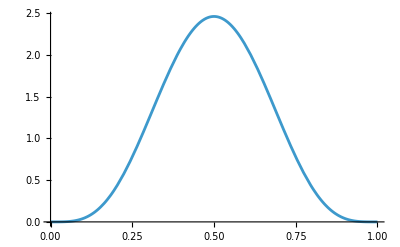

```mathematica
Subscript[α, e]=Subscript[β, e]=5;
Plot[PriorP[x,Subscript[α, e],Subscript[β, e]], {x,0,1}]
```

```mathematica
nbEvidences = 30;evidences = Table[SampleFlip[5, 0.7], nbEvidences]
```

{{2,3},{4,1},{3,2},{4,1},{3,2},{2,3},{2,3},{1,4},{3,2},{4,1},{4,1},{3,2},{4,1},{1,4},{3,2},{4,1},{3,2},{3,2},{5,0},{4,1},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{2,3},{4,1}}

```mathematica
evidencesS = Table[Sum[evidences[[i]],{i,1,j}],{j,1,nbEvidences}] ;
```

```mathematica
Animate[Plot[PriorP[x, Subscript[α, e]+evidencesS[[i]][[1]],Subscript[β, e]+evidencesS[[i]][[2]]], {x,0,1},
PlotRange->All,
PlotLabel->"nb evidence = " <>ToString[i]],
{i, 1, nbEvidences, 1},
AnimationRunning->False]
```